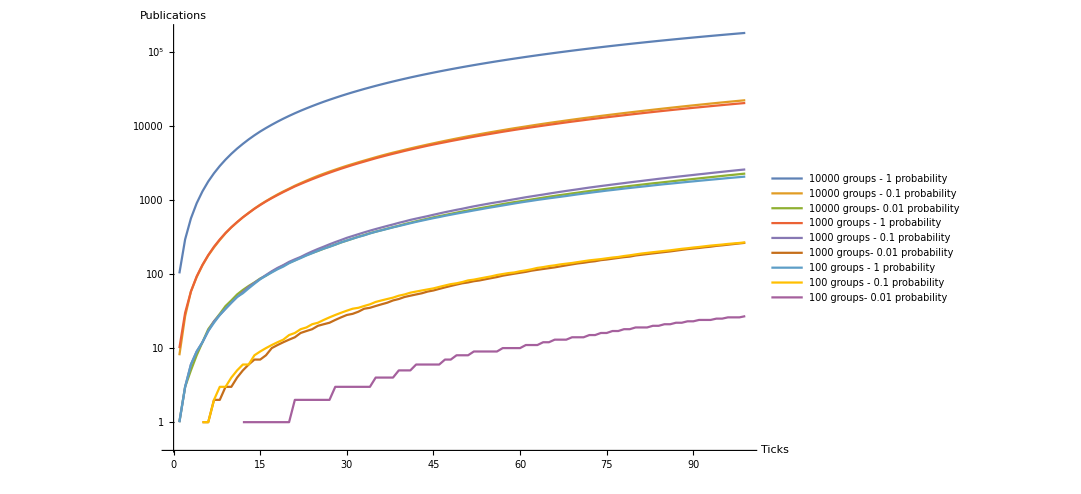

```mathematica
list=Import["/home/fabianact/newTest/NuevoModelo/ModeloSinAcumulacion/averageResults/All.csv"];
plot = Show[ListLogPlot[Partition[list, 100],ImageSize->800,  AxesLabel->{"Ticks","Publications"},Joined->True, PlotLegends->{"10000 groups - 1 probability", "10000 groups - 0.1 probability", "10000 groups- 0.01 probability", "1000 groups - 1 probability", "1000 groups - 0.1 probability", "1000 groups- 0.01 probability","100 groups - 1 probability", "100 groups - 0.1 probability", "100 groups- 0.01 probability", },PlotRange->All]]
Export["TotalSinAcumulacion.png",plot];
```